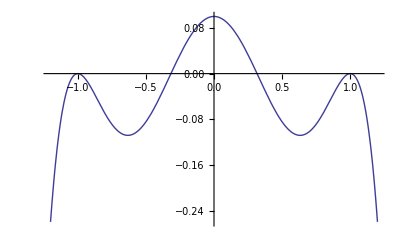

-0.316228

3.83908

-0.0000581336

-0.0209232

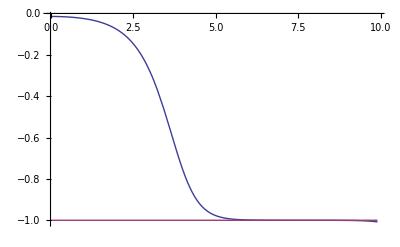

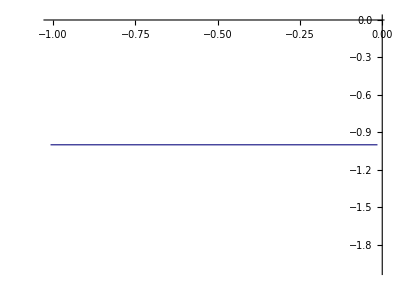

```mathematica
Needs["VariationalMethods`"];
Needs["DifferentialEquations`NDSolveProblems`"];
Needs["DifferentialEquations`NDSolveUtilities`"];
gamma=1/10;
delta1=1/10;
delta2=1/10;
eps=0.301690128;
tmin=0.001;
tmax=9.9;
V[x[t_],y[t_]]:=(x[t]^2-1)^2(x[t]^2-delta1)+((y[t]^2-1)^2-(delta2(y[t]-2)(y[t]+1)^2)/4)/(x[t]^2+gamma);
U[x_,y_]:=(x^2-1)^2(x^2-delta1)+((y^2-1)^2-delta2(y-2)(y+1)^2/4)/(x^2+gamma);
ftn=2*Pi*t*(1/2(D[x[t],t]^2+D[y[t],t]^2)+V[x[t],y[t]]); (* Le Lagrangien *)
Veff[x_]:=U[x,-1];
Plot[-Veff[x],{x,-1.2,1.2}]
x0=x/.FindRoot[Veff[x]==U[-1,-1],{x,-0.3}]
sln=EulerEquations[ftn,{x[t],y[t]},t];
solution=NDSolve[{sln,x[tmin]==x0+eps,y'[tmin]==0,x'[tmax]==-((1+x[tmax]) (1+4 √(2-2 delta1) tmax))/(2 tmax),y[tmax]==-1},{x[t],y[t]},{t,tmin,tmax},Method->{"Shooting","StartingInitialConditions"->{x[tmin]==x0+eps,x'[tmin]==0,y[tmin]==-1,y'[tmin]==0}},MaxSteps->300000];
psi[t_]=x[t]/.solution[[1,1]];
phi[t_]=y[t]/.solution[[1,2]];
action=NIntegrate[2*Pi*t(1/2(D[psi[t],t]^2+D[phi[t],t]^2)+((psi[t]^2-1)^2(psi[t]^2-delta1)+((phi[t]^2-1)^2-delta2(phi[t]-2)(phi[t]+1)^2/4)/(psi[t]^2+gamma))),{t,tmin,tmax}]
psi'[tmin]
psi'[tmax]
lp2=Plot[{psi[t],phi[t]},{t,tmin,tmax},PlotRange->All]
sep=ParametricPlot[{psi[t],phi[t]},{t,tmin,tmax},PlotRange->All]
```

```mathematica
action
```

3.84073